```mathematica
ProductHermitian[v1_, v2_, α_, τ_]:= Conjugate[v1].{{Cos[α-τ]^2+Sin[τ]^2,-2 ⅈ Sin[α] Sin[τ]^2},{2 ⅈ Sin[α] Sin[τ]^2,Cos[α+τ]^2+Sin[τ]^2}}.Transpose[v2] Sec[α]^2
Evolution= {{Cos[τ-α],-ⅈ*Sin[τ]},{-ⅈ*Sin[τ],Cos[α+τ]}}*Sec[α]
EvolutionConjugated= Transpose[{{Cos[τ-α],ⅈ*Sin[τ]},{ⅈ*Sin[τ],Cos[α+τ]}}*Sec[α]]
v1Probe ={{1/(√2),ⅈ/(√2)}}
v2Probe = {{1/(√2),-ⅈ/(√2)}}
v3Probe ={{Cos[ρ/2],ⅈ Sin[ρ/2]}}
cos12=FullSimplify[(ProductHermitian[v1Probe,v2Probe,α, τ])^2/(ProductHermitian[v1Probe,v1Probe,α, τ]*ProductHermitian[v2Probe,v2Probe,α, τ])]
cos13=FullSimplify[(ProductHermitian[v1Probe,v3Probe,α, τ])^2/(ProductHermitian[v1Probe,v1Probe,α, τ]*ProductHermitian[v3Probe,v3Probe,α, τ]),{ρ∈ Reals}]
cos23 =FullSimplify[(ProductHermitian[v2Probe,v3Probe,α, τ])^2/(ProductHermitian[v2Probe,v2Probe,α, τ]*ProductHermitian[v3Probe,v3Probe,α, τ]),{ρ∈ Reals}]
```

{{Cos[α-τ] Sec[α],-ⅈ Sec[α] Sin[τ]},{-ⅈ Sec[α] Sin[τ],Cos[α+τ] Sec[α]}}

{{Cos[α-τ] Sec[α],ⅈ Sec[α] Sin[τ]},{ⅈ Sec[α] Sin[τ],Cos[α+τ] Sec[α]}}

{{1/(√2),ⅈ/(√2)}}

{{1/(√2),-ⅈ/(√2)}}

{{Cos[ρ/2],ⅈ Sin[ρ/2]}}

{{(4 Sin[α]^2 Sin[2 τ]^2)/(3+Cos[2 α]-2 Cos[4 τ] Sin[α]^2)}}

{{(2 (Cos[ρ/2] (Cos[α-τ]^2+(1+2 Sin[α]) Sin[τ]^2)+Sin[ρ/2] (Cos[α+τ]^2+(1+2 Sin[α]) Sin[τ]^2))^2)/((Cos[α-τ]^2+Cos[α+τ]^2+2 (1+2 Sin[α]) Sin[τ]^2) (2+Cos[α-ρ]-Cos[α+ρ]-2 Cos[2 τ] Sin[α] (Sin[α]+Sin[ρ])+Cos[ρ] Sin[2 α] Sin[2 τ]))}}

{{(2 (Cos[ρ/2] (Cos[α-τ]^2+(1-2 Sin[α]) Sin[τ]^2)-Sin[ρ/2] (Cos[α+τ]^2+(1-2 Sin[α]) Sin[τ]^2))^2)/((Cos[α-τ]^2+Cos[α+τ]^2+2 (1-2 Sin[α]) Sin[τ]^2) (2+Cos[α-ρ]-Cos[α+ρ]-2 Cos[2 τ] Sin[α] (Sin[α]+Sin[ρ])+Cos[ρ] Sin[2 α] Sin[2 τ]))}}

```mathematica
cos12F[α_,τ_,ρ_]:=(4 Sin[α]^2 Sin[2 τ]^2)/(3+Cos[2 α]-2 Cos[4 τ] Sin[α]^2)
cos13F[α_,τ_,ρ_]:=(2 (Cos[ρ/2] (Cos[α-τ]^2+(1+2 Sin[α]) Sin[τ]^2)+Sin[ρ/2] (Cos[α+τ]^2+(1+2 Sin[α]) Sin[τ]^2))^2)/((Cos[α-τ]^2+Cos[α+τ]^2+2 (1+2 Sin[α]) Sin[τ]^2) (2+Cos[α-ρ]-Cos[α+ρ]-2 Cos[2 τ] Sin[α] (Sin[α]+Sin[ρ])+Cos[ρ] Sin[2 α] Sin[2 τ]))
cos23F[α_,τ_,ρ_]:=(2 (Cos[ρ/2] (Cos[α-τ]^2+(1-2 Sin[α]) Sin[τ]^2)-Sin[ρ/2] (Cos[α+τ]^2+(1-2 Sin[α]) Sin[τ]^2))^2)/((Cos[α-τ]^2+Cos[α+τ]^2+2 (1-2 Sin[α]) Sin[τ]^2) (2+Cos[α-ρ]-Cos[α+ρ]-2 Cos[2 τ] Sin[α] (Sin[α]+Sin[ρ])+Cos[ρ] Sin[2 α] Sin[2 τ]))
```

```mathematica
vector1={{1/(√2),ⅈ/(√2)}}
vector2={{1/(√2),-ⅈ/(√2)}}
vectorRef={{Cos[ρ/2],ⅈ Sin[ρ/2]}}
Unit={{1,0},{0,1}}
Evolution= {{Cos[τ-α],-ⅈ*Sin[τ]},{-ⅈ*Sin[τ],Cos[α+τ]}}*Sec[α]

τPerp =π/2
ω=1
```

{{1/(√2),ⅈ/(√2)}}

{{1/(√2),-ⅈ/(√2)}}

{{Cos[ρ/2],ⅈ Sin[ρ/2]}}

{{1,0},{0,1}}

{{Cos[α-τ] Sec[α],-ⅈ Sec[α] Sin[τ]},{-ⅈ Sec[α] Sin[τ],Cos[α+τ] Sec[α]}}

π/2

1

```mathematica
EvolutionMT={{Cos[α+τ] Sec[α],ⅈ Sec[α] Sin[τ]},{ⅈ Sec[α] Sin[τ],Cos[α-τ] Sec[α]}}
```

{{Cos[α+τ] Sec[α],ⅈ Sec[α] Sin[τ]},{ⅈ Sec[α] Sin[τ],Cos[α-τ] Sec[α]}}

```mathematica
LeftEvolutionMT={{Cos[α+τ] Sec[α],-ⅈ *Sec[α] Sin[τ]},{-ⅈ *Sec[α] Sin[τ],Sec[α] Cos[α-τ]}}
```

{{Cos[α+τ] Sec[α],-ⅈ Sec[α] Sin[τ]},{-ⅈ Sec[α] Sin[τ],Cos[α-τ] Sec[α]}}

```mathematica
Unit={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
Nm=(N0*FullSimplify[LeftEvolutionMT.EvolutionMT])
ZetaF=MatrixPower[Nm-Unit,1/2]
```

{{N0 Sec[α]^2 (Cos[α+τ]^2+Sin[τ]^2),-2 ⅈ N0 Sec[α] Sin[τ]^2 Tan[α]},{2 ⅈ N0 Sec[α] Sin[τ]^2 Tan[α],N0 Sec[α]^2 (Cos[α-τ]^2+Sin[τ]^2)}}

{{(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)),(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))},{-(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)),(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))}}

```mathematica
Evolution.Transpose[vectorRef]
```

{{Cos[ρ/2] Cos[α-τ] Sec[α]+Sec[α] Sin[ρ/2] Sin[τ]},{ⅈ Cos[α+τ] Sec[α] Sin[ρ/2]-ⅈ Cos[ρ/2] Sec[α] Sin[τ]}}

```mathematica
ZetaF.Evolution.Transpose[vectorRef]
```

{{ⅈ Sin[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α+τ] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+Cos[ρ/2] (Cos[α-τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))},{Cos[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α-τ] Sec[α] (-(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+ⅈ Sin[ρ/2] (Cos[α+τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 N0+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 N0 Cos[α-τ]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 N0-N0 Cos[2 α-2 τ]+2 N0 Cos[2 τ]-N0 Cos[2 α+2 τ]+2 N0 Cos[α-τ]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] (-(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]-2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √((-2+4 N0-2 Cos[2 α]+N0 Cos[2 α-2 τ]-2 N0 Cos[2 τ]+N0 Cos[2 α+2 τ]+2 √2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))/(1+Cos[2 α])) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))}}

```mathematica
FirstPart[M0_,α_,τ_,ρ_]:=Abs[ⅈ Cos[α+τ] Sec[α] Sin[ρ/2]-ⅈ Cos[ρ/2] Sec[α] Sin[τ]]^2+Abs[Cos[ρ/2] Cos[α-τ] Sec[α]+Sec[α] Sin[ρ/2] Sin[τ]]^2
```

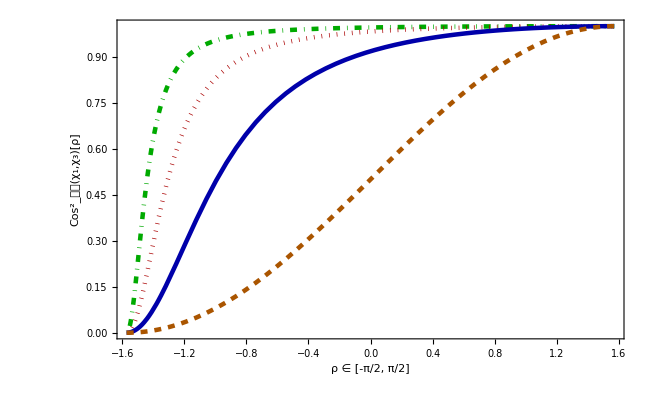

```mathematica
p1=Plot[{cos13F[π/2-0.5,π/2,ρ],cos13F[π/2-0.7,π/2,ρ],cos13F[π/2-1,π/2,ρ],cos13F[0,π/2,ρ] },{ρ,-π/2,π/2},PlotRange->All, PlotStyle->{Directive[Darker[Green], Thickness[0.005],DotDashed],Directive[Darker[Red], Thickness[0.005],Dotted],Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"ρ ∈ [-π/2, π/2]","(Cos^2)_𝒫𝒯(χ_1,χ_3)[ρ]"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

```mathematica
SecondPart[M0_,α_,τ_,ρ_]:=(Abs[ⅈ Sin[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α+τ] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+Cos[ρ/2] (Cos[α-τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))])^2+(Abs[Cos[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α-τ] Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+ⅈ Sin[ρ/2] (Cos[α+τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))])^2
```

```mathematica
Decisiveness=FirstPart[N0,α,τPerp,ρ]/(FirstPart[N0,α,τPerp,ρ]+SecondPart[N0,α,τPerp,ρ])
```

(Abs[Sec[α] Sin[ρ/2]+Cos[ρ/2] Tan[α]]^2+Abs[-ⅈ Cos[ρ/2] Sec[α]-ⅈ Sin[ρ/2] Tan[α]]^2)/(Abs[Sec[α] Sin[ρ/2]+Cos[ρ/2] Tan[α]]^2+Abs[-ⅈ Cos[ρ/2] Sec[α]-ⅈ Sin[ρ/2] Tan[α]]^2+Abs[Cos[ρ/2] (Tan[α] (-(ⅈ N0 (1+Cos[2 α]) Sec[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(N0^2 Sin[α]^2))+(ⅈ N0 (1+Cos[2 α]) Sec[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(N0^2 Sin[α]^2)))-ⅈ Sec[α] (1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2)+1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2)))+ⅈ Sin[ρ/2] (-ⅈ Sec[α] (-(ⅈ N0 (1+Cos[2 α]) Sec[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(N0^2 Sin[α]^2))+(ⅈ N0 (1+Cos[2 α]) Sec[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(N0^2 Sin[α]^2)))-Tan[α] (1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2)+1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2)))]^2+(Abs[Cos[ρ/2] (Tan[α] (1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2)+1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))-ⅈ Sec[α] ((ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))-(ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))))+ⅈ Sin[ρ/2] (-ⅈ Sec[α] (1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2)+1/(16 √2 √(N0^2 Sin[α]^2))√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))-Tan[α] ((ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))-(ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))))])^2)

```mathematica
DecisiveProbability[M0_,α_,τPerp_,ρ_]:=(Abs[Sec[α] Sin[ρ/2]+Cos[ρ/2] Tan[α]]^2+Abs[-ⅈ Cos[ρ/2] Sec[α]-ⅈ Sin[ρ/2] Tan[α]]^2)/(Abs[Sec[α] Sin[ρ/2]+Cos[ρ/2] Tan[α]]^2+Abs[-ⅈ Cos[ρ/2] Sec[α]-ⅈ Sin[ρ/2] Tan[α]]^2+Abs[Cos[ρ/2] (Tan[α] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(M0^2 Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(M0^2 Sin[α]^2)))-ⅈ Sec[α] ((1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2)+(1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)))+ⅈ Sin[ρ/2] (-ⅈ Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(M0^2 Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) Tan[α])/(4 √2 √(M0^2 Sin[α]^2)))-Tan[α] ((1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2)+(1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)))]^2+(Abs[Cos[ρ/2] (Tan[α] ((1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2)+(1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2))-ⅈ Sec[α] ((1/(64 √2 M0 (1+Cos[2 α]) √(M0^2 Sin[α]^2)))ⅈ Cos[α] Cot[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)-(1/(64 √2 M0 (1+Cos[2 α]) √(M0^2 Sin[α]^2)))ⅈ Cos[α] Cot[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)))+ⅈ Sin[ρ/2] (-ⅈ Sec[α] ((1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2)+(1/(16 √2 √(M0^2 Sin[α]^2)))√((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2))-Tan[α] ((1/(64 √2 M0 (1+Cos[2 α]) √(M0^2 Sin[α]^2)))ⅈ Cos[α] Cot[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]-8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)-(1/(64 √2 M0 (1+Cos[2 α]) √(M0^2 Sin[α]^2)))ⅈ Cos[α] Cot[α] √((-2+6 M0-2 Cos[2 α]-2 M0 Cos[2 α]+8 √(M0^2 Sin[α]^2))/(1+Cos[2 α])) (6 M0-2 M0 Cos[2 α]-2 M0 Sec[α]^2-2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)-2 M0 Tan[α]^2-2 M0 Cos[2 α] Tan[α]^2) (-6 M0+2 M0 Cos[2 α]+2 M0 Sec[α]^2+2 M0 Cos[2 α] Sec[α]^2+8 √(M0^2 Sin[α]^2)+2 M0 Tan[α]^2+2 M0 Cos[2 α] Tan[α]^2)))])^2)
```

```mathematica
M01=400.
M02=100.
M03=43.85964912280702
M04=24.36647173489279
M05=15.35
M07=7.51
M10=3.3506871002735
M12=2.1371173469387754
```

400.

100.

43.8596

24.3665

15.35

7.51

3.35069

2.13712

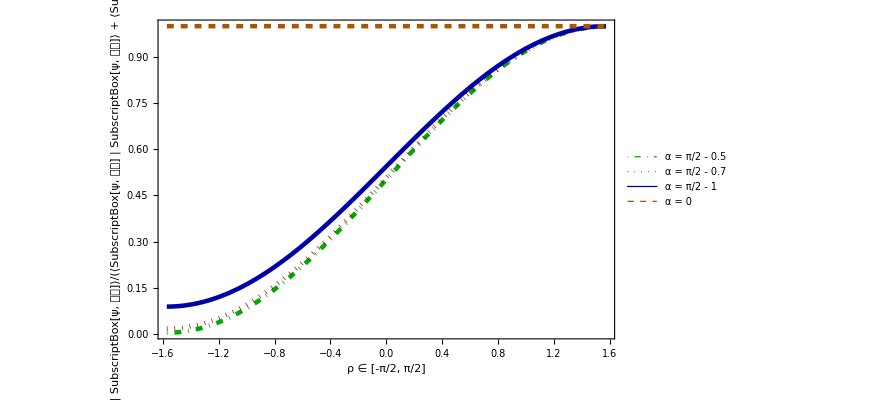

```mathematica
p2=Plot[{DecisiveProbability[M05,π/2-0.5,τPerp,ρ],DecisiveProbability[M07,π/2-0.7,τPerp,ρ],DecisiveProbability[M10,π/2-1,τPerp,ρ],1 },{ρ,-π/2,π/2},PlotRange->All, PlotStyle->{Directive[Darker[Green], Thickness[0.005],DotDashed],Directive[Darker[Red], Thickness[0.005],Dotted],Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"α = π/2 - 0.5","α = π/2 - 0.7","α = π/2 - 1","α = 0"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"ρ ∈ [-π/2, π/2]","Population of postselected space, \n ⟨SubscriptBox[ψ, 𝒫𝒯] | SubscriptBox[ψ, 𝒫𝒯]⟩/(⟨SubscriptBox[ψ, 𝒫𝒯] | SubscriptBox[ψ, 𝒫𝒯]⟩ + ⟨SubscriptBox[ψ, 𝒫𝒯] | SuperscriptBox[ζ, 2] | SubscriptBox[ψ, 𝒫𝒯]⟩)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

```mathematica
ZetaPart1[M0_,α_,τ_,ρ_]:=ⅈ Sin[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α+τ] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+Cos[ρ/2] (Cos[α-τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] ((ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))-(ⅈ Cos[α] Cot[α] Csc[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(32 M0 (1+Cos[2 α]) √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))
```

```mathematica
ZetaPart2[M0_,α_,τ_,ρ_]:=Cos[ρ/2] (-ⅈ Sec[α] Sin[τ] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+Cos[α-τ] Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))+ⅈ Sin[ρ/2] (Cos[α+τ] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (4 M0+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 M0 Cos[α-τ]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2-2 M0 Sec[α]^2 Sin[τ]^2-2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) (-4 M0-M0 Cos[2 α-2 τ]+2 M0 Cos[2 τ]-M0 Cos[2 α+2 τ]+2 M0 Cos[α-τ]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-τ]^2 Sec[α]^2+2 M0 Sec[α]^2 Sin[τ]^2+2 M0 Cos[2 α] Sec[α]^2 Sin[τ]^2+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))/(8 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))-ⅈ Sec[α] Sin[τ] (-((ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]-2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2)))+(ⅈ M0 (1+Cos[2 α]) Sec[α] Sin[τ]^2 √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 τ]-2 M0 Cos[2 τ]+M0 Cos[2 α+2 τ]+2 √2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))) Tan[α])/(2 √(M0^2 (6+2 Cos[2 α]+Cos[2 α-2 τ]-2 Cos[2 τ]+Cos[2 α+2 τ]) Sin[α]^2 Sin[τ]^2))))
```

```mathematica
ZetaPart1[N0,α,π/2,ρ]
```

Cos[ρ/2] (Tan[α] ((√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2))/(16 √2 √(N0^2 Sin[α]^2))+(√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(16 √2 √(N0^2 Sin[α]^2)))-ⅈ Sec[α] ((ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))-(ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))))+ⅈ Sin[ρ/2] (-ⅈ Sec[α] ((√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2))/(16 √2 √(N0^2 Sin[α]^2))+(√((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(16 √2 √(N0^2 Sin[α]^2)))-Tan[α] ((ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]-8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))-(ⅈ Cos[α] Cot[α] √((-2+6 N0-2 Cos[2 α]-2 N0 Cos[2 α]+8 √(N0^2 Sin[α]^2))/(1+Cos[2 α])) (6 N0-2 N0 Cos[2 α]-2 N0 Sec[α]^2-2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)-2 N0 Tan[α]^2-2 N0 Cos[2 α] Tan[α]^2) (-6 N0+2 N0 Cos[2 α]+2 N0 Sec[α]^2+2 N0 Cos[2 α] Sec[α]^2+8 √(N0^2 Sin[α]^2)+2 N0 Tan[α]^2+2 N0 Cos[2 α] Tan[α]^2))/(64 √2 N0 (1+Cos[2 α]) √(N0^2 Sin[α]^2))))

```mathematica
Constraint1[α_,τ_]:=(1+Cos[2 α])/(2-Cos[2 τ]+Cos[2 α] Cos[2 τ]+2 Sin[α] √(3+Cos[2 α]-2 Cos[2 τ] Sin[α]^2) Sin[τ])
Constraint2[α_,τ_]:=(1+Cos[2 α])/(2-Cos[2 τ]+Cos[2 α] Cos[2 τ]-2 Sin[α] √(3+Cos[2 α]-2 Cos[2 τ] Sin[α]^2) Sin[τ])
Constraint3[α_,τ_]:=(2 Cos[α]^2 Sin[α] √(3+Cos[2 α]-2 Cos[2 τ] Sin[α]^2) Sin[τ])/(1-Cos[2 τ] Sin[α]^2-Sin[α] √(3+Cos[2 α]-2 Cos[2 τ] Sin[α]^2) Sin[τ])
```

```mathematica
DecisiveProbabilityPrime[α_,ρ_]:=(3-Cos[2 α]+4 Sin[α] Sin[ρ])/(3-Cos[2 α]+4 Sin[α])
```

```mathematica
N0=Constraint1[α,π/2]
τ=π/2
```

(1+Cos[2 α])/(3-Cos[2 α]+2 Sin[α] √(3+Cos[2 α]+2 Sin[α]^2))

π/2

```mathematica
FullSimplify[ZetaF,-π/2<α<0]
```

{{√2 √(1/(-4+(-3+Cos[2 α]) Csc[α])),ⅈ √2 √(1/(-4+(-3+Cos[2 α]) Csc[α]))},{-ⅈ √2 √(1/(-4+(-3+Cos[2 α]) Csc[α])),√2 √(1/(-4+(-3+Cos[2 α]) Csc[α]))}}

```mathematica
FullSimplify[√((-Sin[α])/(2(1+2 Sin[α]+ Sin[α]^2)))-√(1/(-4+(-3+Cos[2 α]) Csc[α]))]
```

0

```mathematica
ZetaF = (√(-Sin[α]))/(1+Sin[α])*{{ 1,ⅈ },{-ⅈ  , 1}}
```

{{(√(-Sin[α]))/(1+Sin[α]),(ⅈ √(-Sin[α]))/(1+Sin[α])},{-(ⅈ √(-Sin[α]))/(1+Sin[α]),(√(-Sin[α]))/(1+Sin[α])}}

```mathematica
FullSimplify[((Evolution.Transpose[vectorRef])[[1]][[1]]^2+FullSimplify[I*(Evolution.Transpose[vectorRef])[[2]][[1]]]^2)/((Evolution.Transpose[vectorRef])[[1]][[1]]^2+FullSimplify[I*(Evolution.Transpose[vectorRef])[[2]][[1]]]^2+FullSimplify[(ZetaF.Evolution.Transpose[vectorRef])[[1]][[1]]]^2+FullSimplify[I*(ZetaF.Evolution.Transpose[vectorRef])[[2]][[1]]]^2)]
```

(-3+Cos[2 α]-4 Sin[α] Sin[ρ])/(-3+Cos[2 α]+4 Sin[α])